## HW 8

Shahaf Zohar 205978000
Roey Salah 206115438‏

#### Function from the class

```mathematica
SetDirectory[NotebookDirectory[]];
PacletUninstall["IGraphM"];
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"];
<<"IGraphM`";
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
(*Need to install this packet:*)
<<"IGraphM`";
IGVersion[];
CommunityDetectionIGM[graph_,title_String]:=Module[{cl,clcl,len,tot,plot},
cl=IGCommunitiesMultilevel[graph];
clcl=cl["Communities"];
len=Length[clcl];
tot=Table[Length[clcl[[i]]],{i,1,Length[clcl]}];
plot=BarChart[tot,ChartLabels->Range[Length[clcl]],ChartStyle->"Pastel",LabelingFunction->(Placed[#,Center]&),PlotLabel->Row[{"Community detection - ",title," model"}]];
Return[plot];]
```

```mathematica
Pmatrix[graph_,nodesTribe_]:=Module[{numTribes,pMatrix,sizes,i,j},
(*Let K(A,B) be the number of edges between 
tribe A to B, |A| and |B| the sizes of tribes A and B.
Then the probability P_{A,B} for edge between node
 from tribe A to node from tribe B is
P_{A,B}=K(A,B)/(|A||B|) , if A=B then:
P_{A,A}=K(A,A)/Binom(|A|,2)*)
numTribes=Length[DeleteDuplicates[nodesTribe]];
pMatrix=ConstantArray[0,{numTribes,numTribes}];
Scan[If[PropertyValue[{graph,First[#]},"Tribe"]!=PropertyValue[{graph,Last[#]},"Tribe"],{pMatrix[[PropertyValue[{graph,Last[#]},"Tribe"],PropertyValue[{graph,First[#]},"Tribe"]]]++,pMatrix[[PropertyValue[{graph,First[#]},"Tribe"],PropertyValue[{graph,Last[#]},"Tribe"]]]++},pMatrix[[PropertyValue[{graph,First[#]},"Tribe"],PropertyValue[{graph,Last[#]},"Tribe"]]]++]&,EdgeList[graph]];
(*calculate |tribe|*)
sizes=Table[Count[nodesTribe,i],{i,1,numTribes}];
(*divide by n to get P_ij probability*)
For[i=1,i<=numTribes,i++,
For[j=1,j<=numTribes,j++,
If[i==j,pMatrix[[i,j]]=pMatrix[[i,j]]/Binomial[sizes[[i]],2]//N;,pMatrix[[i,j]]=pMatrix[[i,j]]/(sizes[[i]]*sizes[[j]])//N];

]
];
pMatrix
]
(*create Random Block Model*)
BlockModel[graph_,pMat_]:=Module[{B,adjMat,pEdge,n,i,j,tribeA,tribeB},
(*Loop over all combination of 2 nodes, for each 2 node, the first from tribe A and the second from tribe B, I check the P_matrix for the probability for such edge 
and update in adjancency matrix*)
n=VertexCount[graph];
adjMat=ConstantArray[0,{n,n}];
For[i=1,i<n,i++,
tribeA=PropertyValue[{graph,VertexList[graph][[i]]},"Tribe"];
For[j=i+1,j<=n,j++,
tribeB=PropertyValue[{graph,VertexList[graph][[j]]},"Tribe"];
pEdge=pMat[[tribeA,tribeB]];
If[RandomReal[]<=pEdge,
{adjMat[[i,j]]=1;
adjMat[[j,i]]=1;}
]
]
];
B=AdjacencyGraph[VertexList[graph],adjMat,GraphLayout->"CircularEmbedding"];
Return[B]
]
(*Shift diagram functions*)
RenameGraphN[g_, sl_]:=Module[{G= g,VrDg = sl,VrLs,VrLst,SVrLst,NewName,edges,NewEdges, ed},
VrLs =VertexList[G];
VrLst = Table[{VrDg[[i]], VrLs[[i]]},{i,Length[VrDg]}];
SVrLst= Sort[VrLst,#1[[1]]>#2[[1]]&];
NewName = Table[SVrLst[[i]][[2]],{i,Length[VrDg]}];
edges = EdgeList[G];
If[DirectedGraphQ[G], 
NewEdges =Table[Position[NewName,edges[[i]][[1]]][[1]][[1]]->Position[NewName,edges[[i]][[2]]][[1]][[1]],{i,Length[edges]}],
NewEdges =Table[Position[NewName,edges[[i]][[1]]][[1]][[1]]<->Position[NewName,edges[[i]][[2]]][[1]][[1]],{i,Length[edges]}]];
Graph[Range[Length[VrLst]],NewEdges]]
SymmetryPoint[G_]:=Module[{s,EE={}, EP={}, PE={},PP={},ee=0,ep=0, pe=0,pp=0,tc, bc, tr,br},
s=Length[VertexList[G]];
ee = AdjacencyMatrix[G][[1]][[1]];
pe = Total[Total[Take[AdjacencyMatrix[G],{2,s},{1,1}]]];
ep = Total[Total[Take[AdjacencyMatrix[G],{1,1},{2,s}]]];
pp = Total[Total[Take[AdjacencyMatrix[G],{2,s},{2,s}]]];
EE= {0,ee/2};
EP ={0,ep/2};
PE= {0,pe/2};
PP= {EdgeCount[G],pp/2};
For[i=1,i < s-1,i++;
tc = Total[Total[Take[AdjacencyMatrix[G],{1,i-1},{i,i}]]];
bc = Total[Total[Take[AdjacencyMatrix[G],{i+1,s},{i,i}]]];
tr = Total[Total[Take[AdjacencyMatrix[G],{i,i},{1,i-1}]]];
br = Total[Total[Take[AdjacencyMatrix[G],{i,i},{i+1,s}]]];
ee = ee + tc + tr+AdjacencyMatrix[G][[i]][[i]];
ep =ep + br -tc;
pe = pe + bc -tr;
pp = pp - bc - br-AdjacencyMatrix[G][[i]][[i]];;
EE =Join[EE,{ee/2}];
EP = Join[EP, {ep/2}];
PE = Join[PE,{pe/2}];
PP = Join[PP, {pp/2}];];
{EE,EP+PE, PP}]
PlotShift[graph_,title_String]:=Module[{a},
a=ListLinePlot[SymmetryPoint[RenameGraphN[graph,VertexDegree[graph]]],PlotLegends->Placed[{"I(ℰ,ℰ)","I(𝒫,ℰ)","I(𝒫,𝒫)"},Bottom],PlotRange->All,AxesLabel->{"Core Size","Number of Edges"},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},PlotLabel->Row[{"Shift diagram - ",title," model"}]];
Return[a];
]
```

### Loading the network

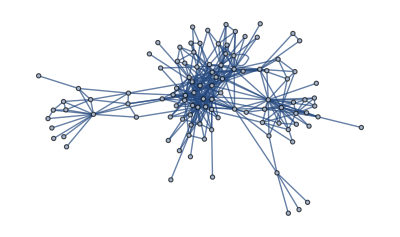

```mathematica
SetDirectory[NotebookDirectory[]];
file=Rest[Import["stormofswords.csv"]];
tribes=Import["tribes.csv"];
nodes=Flatten[tribes⟦All,1⟧];
nodesTribe=Flatten[tribes[[All,2]]];
edges=#⟦1⟧<->#⟦2⟧&/@file[[All,{1,2}]];
G=Graph[nodes,edges]
```

```mathematica
G=SetProperty[{G,VertexList[G]},Thread["Tribe"->nodesTribe]];
PropertyValue[{G,"Daenerys"},"Tribe"]
```

5

#### 1. Using Network of Throne data generate G (n, p), G (n, m), Block model, configuration model

first we creating Random Configuration Model

```mathematica
edgeDensity=EdgeCount[G]/Binomial[VertexCount[G],2]//N
```

0.0622465

Presentation of the models

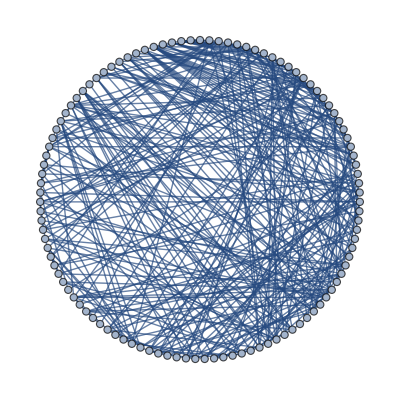
-Graphics-ER Circular

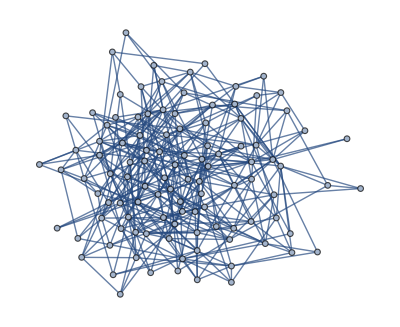
-Graphics-ER Standart

```mathematica
ERCircular=Graph[RandomGraph[BernoulliGraphDistribution[VertexCount[G],edgeDensity],GraphLayout->"CircularEmbedding"]];
Labeled[ERCircular,"ER Circular",Top]
ER=Graph[RandomGraph[BernoulliGraphDistribution[VertexCount[G],edgeDensity]]];
Labeled[ER,"ER Standart",Top]
```

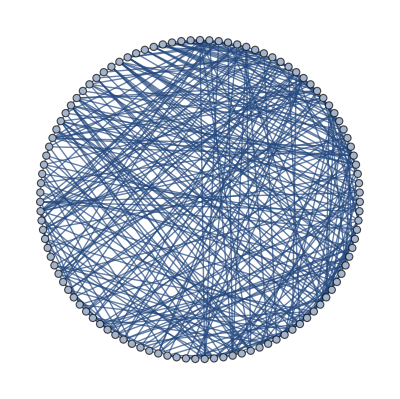
-Graphics-UR Circular

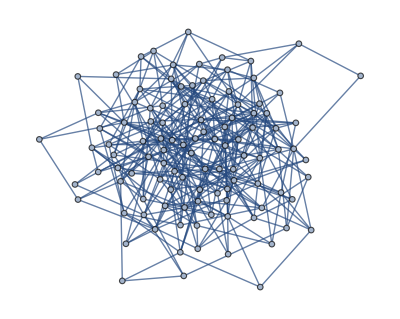
-Graphics-UR Standart

```mathematica
URCircular=RandomGraph[UniformGraphDistribution[VertexCount[G],EdgeCount[G]],GraphLayout->"CircularEmbedding"];
Labeled[URCircular,"UR Circular",Top]
UR=RandomGraph[UniformGraphDistribution[VertexCount[G],EdgeCount[G]]];
Labeled[UR,"UR Standart",Top]
```

```mathematica
(*This functiuon from the class is'nt working *)
```

```mathematica
UR1=RandoGraph[UniformGraphDistribution[VertexCount[G],Binomial[VertexCount[G],2]*1/5],GraphLayout->"CircularEmbedding"]
```

RandoGraph[UniformGraphDistribution[107,5671/5],GraphLayout→CircularEmbedding]

Degree Sequence

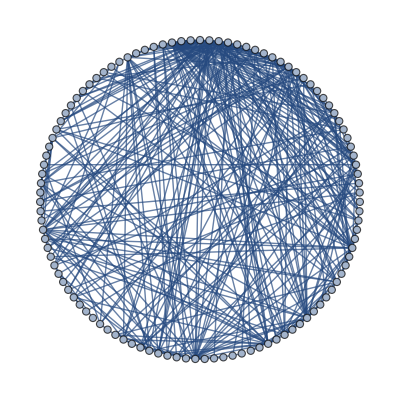
-Graphics-UR Circular

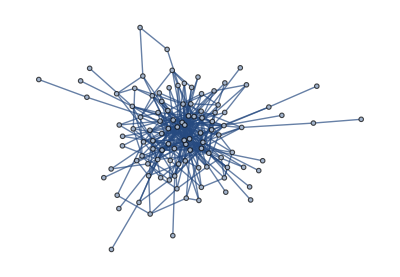
-Graphics-UR Standart

```mathematica
DSCircular = RandomGraph[DegreeGraphDistribution[VertexDegree[G]],GraphLayout->"CircularEmbedding"];
Labeled[DSCircular,"UR Circular",Top]
DS=RandomGraph[DegreeGraphDistribution[VertexDegree[G]]];
Labeled[DS,"UR Standart",Top]
```

Block Model

(0.263158 | 0.0394737 | 0.00438596 | 0.00657895 | 0. | 0.0438596 | 0.0150376
0.0394737 | 0.428571 | 0.0520833 | 0.00625 | 0. | 0. | 0.0714286
0.00438596 | 0.0520833 | 0.424242 | 0.04375 | 0. | 0.0277778 | 0.0595238
0.00657895 | 0.00625 | 0.04375 | 0.166667 | 0.01 | 0.0291667 | 0.0714286
0. | 0. | 0. | 0.01 | 0.247619 | 0. | 0.
0.0438596 | 0. | 0.0277778 | 0.0291667 | 0. | 0.4 | 0.
0.0150376 | 0.0714286 | 0.0595238 | 0.0714286 | 0. | 0. | 0.714286)

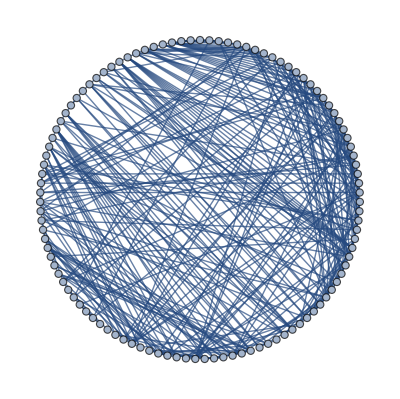
-Graphics-Block Model Circular

```mathematica
blockMatrix=Pmatrix[G,nodesTribe];
MatrixForm[blockMatrix]
BM=BlockModel[G,blockMatrix];
Labeled[BM,"Block Model Circular",Top]
```

### 2. Compare for graphs : Degree Distribution, Giant component, Average distance, Shift Diagram for Core - Periphery, Community Detedction .

## Degree distribution for G(n, p)

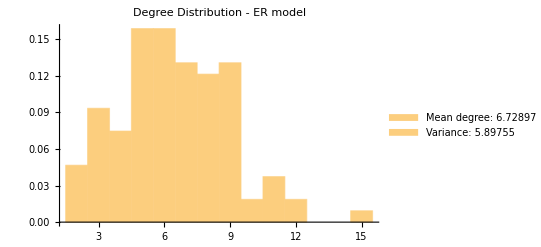

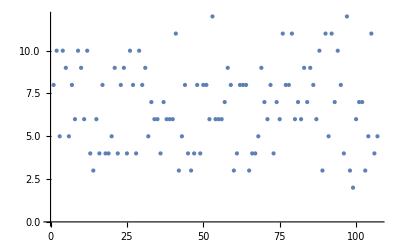

```mathematica
Histogram[VertexDegree[ERCircular],{1},"Probability",PlotLabel->"Degree Distribution - ER model",ChartLegends->Placed[{StringForm["Mean degree: ``",Mean[VertexDegree[ER]]//N],StringForm["Variance: ``",Variance[VertexDegree[ER]]//N]},Bottom]]
ListPlot[Transpose[{Range[Length[VertexDegree[ER]]],VertexDegree[ER]}],PlotStyle->PointSize[Medium]]
```

```mathematica
adjM= AdjacencyMatrix[ER];
graph=AdjacencyGraph[adjM];
giantComponent=SortBy[ConnectedComponents[graph],Length][[-1]];
giantGraph=Subgraph[graph,giantComponent];
(*Giant component*)
GcER = Length[First[ConnectedComponents[ER]]];
Print["Giant component G(n, p) - ",GcER ]
Graph[giantGraph]
```

Giant component G(n, p) - 107

-Graphics-

```mathematica
distanceMatrix=GraphDistanceMatrix[ER];
n=VertexCount[ER];
totalDistance=Total[Flatten[distanceMatrix]];
averageDistance=totalDistance/(n*(n-1));
Print["Average Distance:",averageDistance//N]
```

Average Distance:2.62529

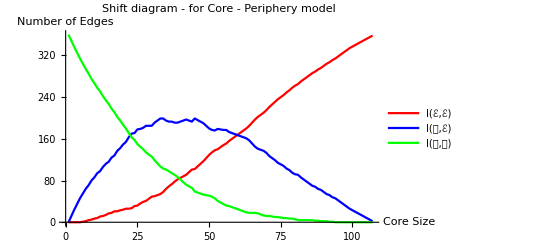

```mathematica
(*Shift diagram*)
UnWight=AdjacencyMatrix[ER];
degrees=Total/@UnWight;
namelistcore =VertexList[ER];
res=RenameGraphN[ER,VertexDegree[ER]];
PlotShift[res,"for Core - Periphery"]
```

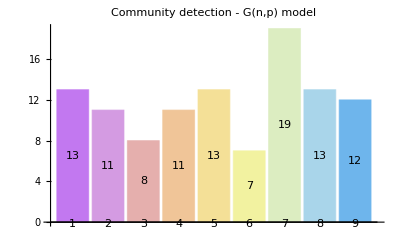

-Graphics-

```mathematica
(*Community Detection*)
CommunityDetectionIGM[ER,"G(n,p)"]
cl=IGCommunitiesMultilevel[ER];
clcl=cl["Communities"];
CommunityGraphPlot[ER,clcl]
```

## Degree distribution for G (n, m)

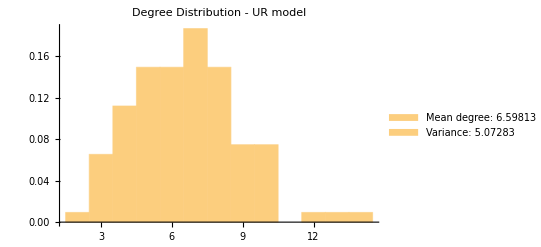

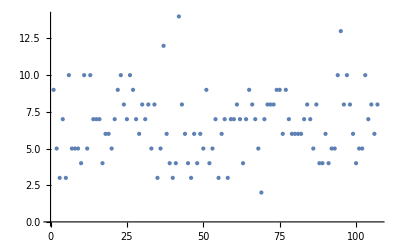

```mathematica
Histogram[VertexDegree[UR],{1},"Probability",PlotLabel->"Degree Distribution - UR model",ChartLegends->Placed[{StringForm["Mean degree: ``",Mean[VertexDegree[UR]]//N],StringForm["Variance: ``",Variance[VertexDegree[UR]]//N]},Bottom]]
ListPlot[Transpose[{Range[Length[VertexDegree[UR]]],VertexDegree[UR]}],PlotStyle->PointSize[Medium]]
```

```mathematica
adjM= AdjacencyMatrix[UR];
graph=AdjacencyGraph[adjM];
giantComponent=SortBy[ConnectedComponents[graph],Length][[-1]];
giantGraph=Subgraph[graph,giantComponent];
(*Giant component*)
GcUR = Length[First[ConnectedComponents[UR]]];
Print["Degree distribution for G(n, m), Giant component G(n, m) - ",GcUR ]
Graph[giantGraph]
```

Degree distribution for G(n, m), Giant component G(n, m) - 107

-Graphics-

```mathematica
distanceMatrix=GraphDistanceMatrix[UR];
n=VertexCount[UR];
totalDistance=Total[Flatten[distanceMatrix]];
averageDistance=totalDistance/(n*(n-1));
Print["Average Distance:",averageDistance//N]
```

Average Distance:2.64063

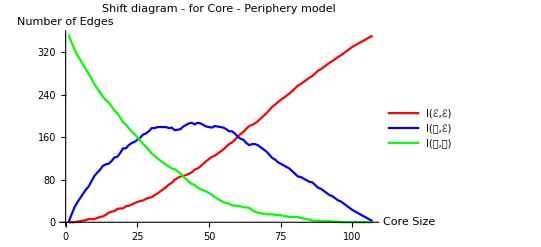

```mathematica
(*Shift diagram*)
UnWight=AdjacencyMatrix[UR];
degrees=Total/@UnWight;
namelistcore =VertexList[UR];
res=RenameGraphN[UR,VertexDegree[UR]];
PlotShift[res,"for Core - Periphery"]
```

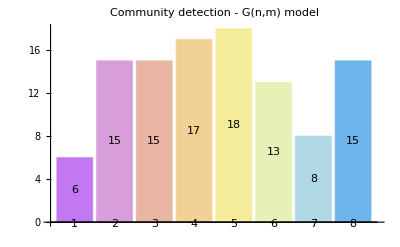

-Graphics-

```mathematica
(*Community Detection*)
CommunityDetectionIGM[ER,"G(n,m)"]
cl=IGCommunitiesMultilevel[UR];
clcl=cl["Communities"];
CommunityGraphPlot[UR,clcl]
```

## Configuration Model

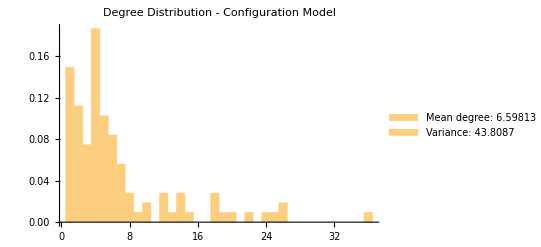

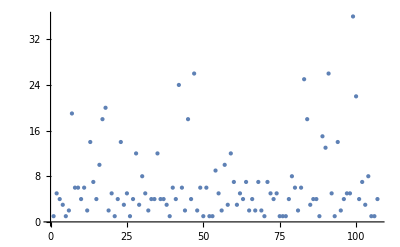

```mathematica
Histogram[VertexDegree[DS],{1},"Probability",PlotLabel->"Degree Distribution - Configuration Model",ChartLegends->Placed[{StringForm["Mean degree: ``",Mean[VertexDegree[DS]]//N],StringForm["Variance: ``",Variance[VertexDegree[DS]]//N]},Bottom]]
ListPlot[Transpose[{Range[Length[VertexDegree[DS]]],VertexDegree[DS]}],PlotStyle->PointSize[Medium]]
```

```mathematica
adjM= AdjacencyMatrix[DS];
graph=AdjacencyGraph[adjM];
giantComponent=SortBy[ConnectedComponents[graph],Length][[-1]];
giantGraph=Subgraph[graph,giantComponent];
(*Giant component*)
GcDS = Length[First[ConnectedComponents[DS]]];
Print["Configuration Model, Giant component- ",GcDS ]
Graph[giantGraph]
```

Configuration Model, Giant component- 107

-Graphics-

```mathematica
distanceMatrix=GraphDistanceMatrix[DS];
n=VertexCount[DS];
totalDistance=Total[Flatten[distanceMatrix]];
averageDistance=totalDistance/(n*(n-1));
Print["Average Distance:",averageDistance//N]
```

Average Distance:2.69564

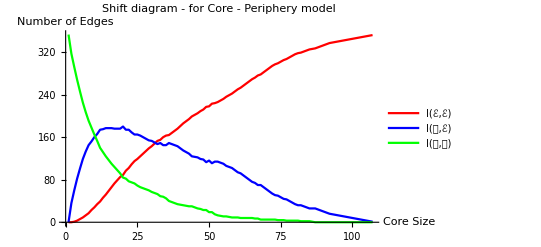

```mathematica
(*Shift diagram*)
UnWight=AdjacencyMatrix[DS];
degrees=Total/@UnWight;
namelistcore =VertexList[DS];
res=RenameGraphN[DS,VertexDegree[DS]];
PlotShift[res,"for Core - Periphery"]
```

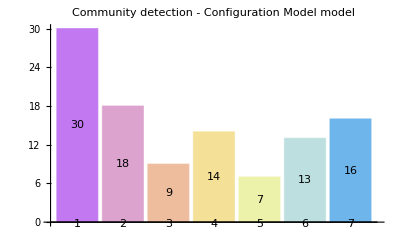

-Graphics-

```mathematica
(*Community Detection*)
CommunityDetectionIGM[ER,"Configuration Model"]
cl=IGCommunitiesMultilevel[DS];
clcl=cl["Communities"];
CommunityGraphPlot[DS,clcl]
```

## Block Model

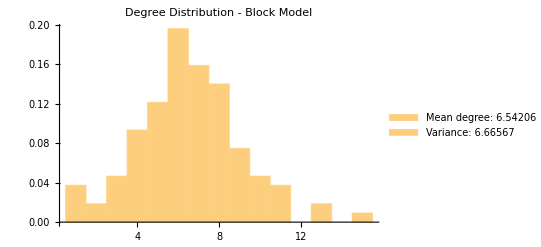

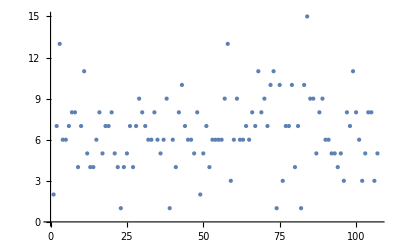

```mathematica
Histogram[VertexDegree[BM],{1},"Probability",PlotLabel->"Degree Distribution - Block Model",ChartLegends->Placed[{StringForm["Mean degree: ``",Mean[VertexDegree[BM]]//N],StringForm["Variance: ``",Variance[VertexDegree[BM]]//N]},Bottom]]
ListPlot[Transpose[{Range[Length[VertexDegree[BM]]],VertexDegree[BM]}],PlotStyle->PointSize[Medium]]
```

Block Model, Giant component- 107

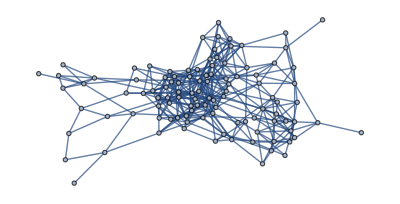

```mathematica
adjM= AdjacencyMatrix[BM];
graph=AdjacencyGraph[adjM];
giantComponent=SortBy[ConnectedComponents[graph],Length][[-1]];
giantGraph=Subgraph[graph,giantComponent];
(*Giant component*)
GcBM= Length[First[ConnectedComponents[BM]]];
Print["Block Model, Giant component- ",GcBM ]
Graph[giantGraph]
```

```mathematica
distanceMatrix=GraphDistanceMatrix[BM];
n=VertexCount[BM];
totalDistance=Total[Flatten[distanceMatrix]];
averageDistance=totalDistance/(n*(n-1));
Print["Average Distance:",averageDistance//N]
```

Average Distance:2.99788

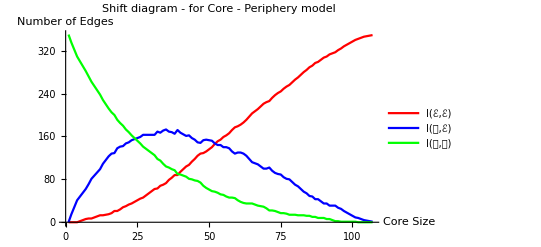

```mathematica
(*Shift diagram*)
UnWight=AdjacencyMatrix[BM];
degrees=Total/@UnWight;
namelistcore =VertexList[BM];
res=RenameGraphN[BM,VertexDegree[BM]];
PlotShift[res,"for Core - Periphery"]
```

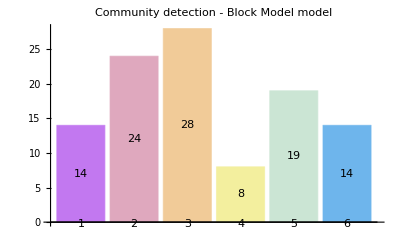

-Graphics-

```mathematica
(*Community Detection*)
CommunityDetectionIGM[BM,"Block Model"]
cl=IGCommunitiesMultilevel[BM];
clclBM=cl["Communities"];
CommunityGraphPlot[BM,clclBM]
```

## Original Graph Throne network

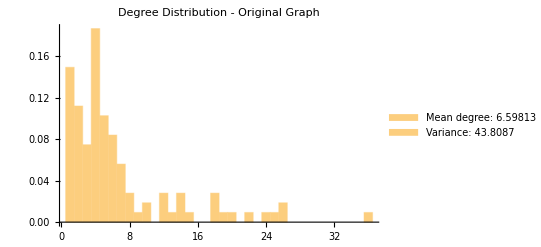

-Graphics-

```mathematica
Histogram[VertexDegree[G],{1},"Probability",PlotLabel->"Degree Distribution - Original Graph",ChartLegends->Placed[{StringForm["Mean degree: ``",Mean[VertexDegree[G]]//N],StringForm["Variance: ``",Variance[VertexDegree[G]]//N]},Bottom]]
ListPlot[Transpose[{Range[Length[VertexDegree[G]]],VertexDegree[G]}],PlotStyle->PointSize[Medium]]
```

```mathematica
adjM= AdjacencyMatrix[G];
graph=AdjacencyGraph[adjM];
giantComponent=SortBy[ConnectedComponents[graph],Length][[-1]];
giantGraph=Subgraph[graph,giantComponent];
(*Giant component*)
GcG = Length[First[ConnectedComponents[G]]];
Print["Configuration Model, Giant component- ",GcG ]
Graph[giantGraph]
```

Configuration Model, Giant component- 107

-Graphics-

```mathematica
distanceMatrix=GraphDistanceMatrix[G];
n=VertexCount[G];
totalDistance=Total[Flatten[distanceMatrix]];
averageDistance=totalDistance/(n*(n-1));
Print["Average Distance:",averageDistance//N]
```

Average Distance:2.9039

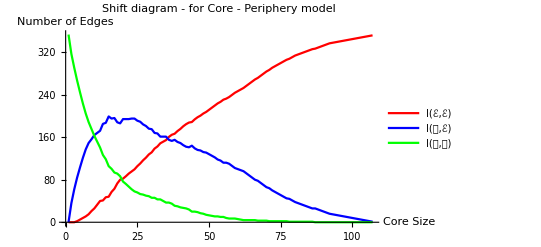

```mathematica
(*Shift diagram*)
UnWight=AdjacencyMatrix[G];
degrees=Total/@UnWight;
namelistcore =VertexList[G];
res=RenameGraphN[G,VertexDegree[G]];
PlotShift[res,"for Core - Periphery"]
```

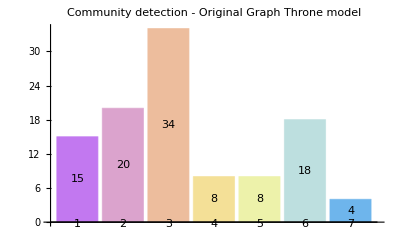

-Graphics-

```mathematica
(*Community Detection*)
CommunityDetectionIGM[G,"Original Graph Throne"]
cl=IGCommunitiesMultilevel[G];
clclG=cl["Communities"];
CommunityGraphPlot[G,clclG]
```

### 3. Discuss your finding, what (and why) are the differences with the original network .

for the discuss models, G (n, p) and G (n, m) models generate random graphs with varying edge configurations, while the block model and configuration model aim to simplify and analyze specific aspects of the original graph, such as community structure or degree distribution, respectively . The choice of model depends on the specific characteristics of the original graph that we want to preserve or explore.

Now we explain the reasons for The differences for each model :

The Reasons for G (n, p): The randomness in edge formation reflects a scenario where connections between nodes are created independently with a given probability . This model is used to study random graphs and analyze their properties, such as connectivity, percolation, and phase transitions

The Reasons for G (n, m): This model allows for controlling the number of edges in the graph while maintaining randomness. It is useful in situations where the desired number of edges is known or needs to be controlled independently of the original network’s specific connectivity patterns.

The Reasons for Block model:‏ The block model is used to uncover structural patterns, community structures, or functional modules within the network. It provides a more abstract view of the network’s organization and facilitates analysis and understanding of complex networks by grouping similar nodes together

The Reasons for configuration: The configuration model is useful when studying the role of degree distribution in a network while disregarding the original network’s specific connectivity patterns. It allows for generating random graphs with a prescribed degree sequence, which can be used for statistical analyses or comparison with other networks

The average distance and giant component are similarly present, and we can see that expected value(Degree) approximately the same for each model and the result is  N*P = 107×0.0622465 ~ 6.6 .
and for the Diameter for all model is the same again and the calculate  D ~ (log(107))/(log(6.6))= 2.476 .  
We can see that is less then log(107) = 4.672 as we expected.

In summary, the differences between the original network and the graph models arise due to the specific generation methods employed by each model . These differences are purposeful and serve different analytical or modeling objectives, such as studying random graphs, understanding community structures, or analyzing degree distributions . The choice of model depends on the research questions or objectives at hand.